```mathematica
ClearAll["`*"]
```

```mathematica
method={FourierSeries, FourierCoefficient};
SetOptions[method,FourierParameters -> {1,2π/(TZero/2)}];
TZero=1/f;
FZero=1/TZero;
f = 220;
```

```mathematica
(*From the question where we want to hear different samplerate*)
x[t_]:=Abs[Sin[2*Pi*f*t]];
Play[x[t],{t,0,1},SampleRate->1000]
Play[x[t],{t,0,1},SampleRate->8000]
```

-Graphics-

-Graphics-

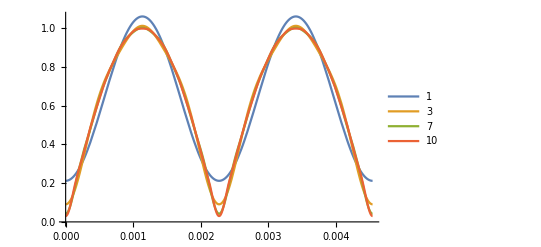

```mathematica
x[t_]:=Abs[Sin[2*Pi*f*t]]
s[t_,k_]:=FourierSeries[x[t],t,k]
Plot[{Evaluate[s[t,1]],Evaluate[s[t,3]],Evaluate[s[t,7]],Evaluate[s[t,10]]},{t,0,TZero}, PlotLegends->{"1" ,"3","7","10"}]
```

```mathematica
fouCoe[k_]:=FourierCoefficient[x[t],t,k]
```

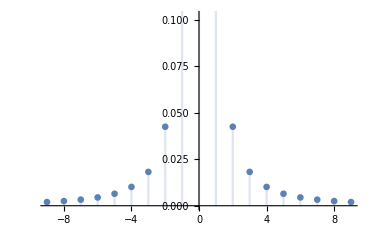

```mathematica
DiscretePlot[Abs[fouCoe[k]],{k,-9,9}]
```